# Building the Throne

Math 213 - Michael DiGiorgio
“Parametric Throne”
Versatile Processed White Plastic

## Description

A 3D throne made from simple stacked polygons, and an ornate headspace and backing designed with parametric equations.

## Building the throne and base

### To start making the throne, we first start with the base, which is done by simply inserting cuboids. The arguments are two lists of XYZ-plane coordinates, which specify from which values the cuboid stretches between. For example:

```mathematica
Graphics3D[
    {Cuboid[{-5,0,-1},{15,12,1}]}]
```

-Graphics3D-

### I’ve made a block that goes from a -5 x-value to 15 (thus a length of 20), a 0 y-value to 12, and a -1 z-value to 1. Lets add a view more and build steps:

```mathematica
Graphics3D[
    { Cuboid[{-5,0,-1},{15,12,1}],
    Cuboid[{0,0,1},{15,12,2}],
Cuboid[{3,0,2},{15,12,3}]}]
```

-Graphics3D-

-Graphics3D-

### In order to make this, I simply inserted more cuboids with the appropriate coordinates. In order to make sure they’re touching properly (stacked), you must make sure that the next cuboid’s z-coordinate begins where the last cuboid’s z coordinate ended. Each cube begins at a larger x-value to make sure it appears as steps. Also, once we have the general shape, we can “hollow” out certain pieces to cut the cost for printing. For example, the “box” of the throne seat, instead of being this...

```mathematica
Graphics3D[Cuboid[{0,0,0},{10,8,9}]]
```

-Graphics3D-

### ...which is a completely solid cube, we can make a number of different “slabs” pieced together with coordinate manipulation to make it hollow. It will be a little more work, but will save on cost:

```mathematica
Graphics3D[{Cuboid[{0,0,0},{5,.8,6}],
		   Cuboid[{0,5,0},{5,5.8,6}],
		   Cuboid[{0,0,6},{5,5.8,7}],
		Cuboid[{3.8,.8,0},{5,5,6}],
}]
```

-Graphics3D-

### We can do this for the armrests, seat, and backboard:

```mathematica
Graphics3D[
    {Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],
    
Cuboid[{15,0,-1},{17,12,22}],
}]
```

-Graphics3D-

### Simple enough, right? Let’s also add the rectangular bar that we’ll add the headpiece on later:

```mathematica
Graphics3D[
    {Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}]}]
```

-Graphics3D-

### Next, we’ll add tubes to the armrest blocks to give them a more throne-y look:

```mathematica
Graphics3D[
    {Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
   
Tube[{{5,1,10},{14.26,1,9.5}},1.2],
Tube[{{5,11,10},{14.26,11,9.5}},1.2]
}]
```

-Graphics3D-

### Notice the slightly different z-coordinates to give them a slightly upward slope. The tubes look okay, however, they will be hollow when we export this file, with holes on either end. We need to end some kind of shapes at either end to make sure they’re not hollow. Let’s import some globes and colorize them so we have a better idea of where they are in space:

```mathematica
Graphics3D[
    {Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
    Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
   
{Green,Sphere[{ 5.2,1,10},1.5]},
Green,Sphere[{ 5.2,11,10},1.5],
Purple,Sphere[{14.265,1,9.5},1.3],
Yellow,Sphere[{14.265,11,9.5},1.3]
}]
```

-Graphics3D-

### The balls were placed at coordinates that would fill in the end points of the tube, so that when printed, will print seamlessly as a full object with gaps. Lastly for the base of the throne, we’ll add rods (tubes) that will support the headpiece, and fill them with a similar method:

```mathematica
Graphics3D[
    {Red,Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Green,Sphere[{ 5.2,1,10},1.5]},
    Green,Sphere[{ 5.2,11,10},1.5],
    Purple,Sphere[{14.265,1,9.5},1.3],
    Yellow,Sphere[{14.265,11,9.5},1.3],

   Red, Tube[{{16,-1,24},{16,3,29}},.75],
   Red, Tube[{{16,13,24},{16,9,29}},.75],

  Green,Sphere[{16,-1,23.7},1],
  Green,Sphere[{16,13,23.7},1],
  Green,Sphere[{16,9,29},.8],
  Green,Sphere[{16,3,29},.8]
}]
```

-Graphics3D-

### Now we have a good base. Let’s save the throne to a variable and add some fun coloring for the whole thing with RGBColor:

```mathematica
redThroneTest = Show[Graphics3D[
    {RGBColor[.4,0,0],Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Sphere[{ 5.2,1,10},1.5],
    Sphere[{ 5.2,11,10},1.5],
    Sphere[{14.265,1,9.5},1.3],
    Sphere[{14.265,11,9.5},1.3],

   Tube[{{16,-1,24},{16,3,29}},.75],
   Tube[{{16,13,24},{16,9,29}},.75],

  Sphere[{16,-1,23.7},1],
  Sphere[{16,13,23.7},1],
  Sphere[{16,9,29},.8],
  Sphere[{16,3,29},.8]



}}]


]
```

-Graphics3D-

## The Spikes

### If objects are close enough together that they cross into their coordinate areas, they will effectively "embed" into one another. When exported as a file for 3D printing, they will be printed as a whole piece, provided they are close enough to each other to mesh into one another. We'll use this particularly in the next section, to add spikes to the top bar using cubes.

### Here we’ll input from PolyHedronData a “Cube” object, then we’ll export and import to discretize.

```mathematica
cube=PolyhedronData[Entity["Polyhedron","Cube"]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"cube.stl",cube]
```

/Users/michaeldigiorgio/Desktop/cube.stl

```mathematica
discreteCube=Import[NotebookDirectory[]<>"cube.stl"]
```

-Graphics3D-

```mathematica
discreteCube=RegionResize[discreteCube,1.1]
```

-Graphics3D-

### We can do some easily translations and rotations with the object as a discrete object. We’ll use TransformedRegion(to indicate what region/object we’re going to modify), TranslationTransform(where it will be moved on the xyz-plane) and RotationTransform to indicate how it will be rotated on the plane:

```mathematica
redThroneTest = Show[Graphics3D[
    {RGBColor[.4,0,0],Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Sphere[{ 5.2,1,10},1.5],
    Sphere[{ 5.2,11,10},1.5],
    Sphere[{14.265,1,9.5},1.3],
    Sphere[{14.265,11,9.5},1.3],

   Tube[{{16,-1,24},{16,3,29}},.75],
   Tube[{{16,13,24},{16,9,29}},.75],

  Sphere[{16,-1,23.7},1],
  Sphere[{16,13,23.7},1],
  Sphere[{16,9,29},.8],
  Sphere[{16,3,29},.8]



}}],

TransformedRegion[TransformedRegion[RegionResize[discreteCube,1.15],RotationTransform[90Degree,{1,1,0}]],TranslationTransform[{10,3,23}]]
]
```

-Graphics3D-

### Well, it imported properly and rotated at least. But it’s not in the same form as the throne, so we’ll extract the polygons from the shape and turn it into a primitive, and also move it into the proper place on the headboard. We want to move the cube halfway “into” the headboard so that it embeds, but sticks out enough to look like a spike. We’ll wrap the whole Graphics3D in a table command to generate 8 copies, all of the same x and z coordinate, but of evenly spaced y coordinates as well:

```mathematica
redThroneTest = Show[Graphics3D[
    {RGBColor[.4,0,0],Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Sphere[{ 5.2,1,10},1.5],
    Sphere[{ 5.2,11,10},1.5],
    Sphere[{14.265,1,9.5},1.3],
    Sphere[{14.265,11,9.5},1.3],

   Tube[{{16,-1,24},{16,3,29}},.75],
   Tube[{{16,13,24},{16,9,29}},.75],

  Sphere[{16,-1,23.7},1],
  Sphere[{16,13,23.7},1],
  Sphere[{16,9,29},.8],
  Sphere[{16,3,29},.8]



}}],

Table[Graphics3D[{RGBColor[.7,.7,.7],MeshPrimitives[TransformedRegion[TransformedRegion[RegionResize[discreteCube,1.15],RotationTransform[90Degree,{1,1,0}]],TranslationTransform[{15.4,i,23}]],2]}],{i, -1,13,2}]
]
```

-Graphics3D-

### It worked! The cubes will appear jutting out as spikes on the discrete model and when it’s printed. Now, let’s get to the two most interesting pieces: the backing and the headboard.

## The Back Emblem

### To make the emblem, which is more ornate than what we’ve made thus far, we’ll have to use parametric equations, in particular ParametricPlot3D to make a full 3D object. To start off simply, let’s see what our shape will look like in 2D first:

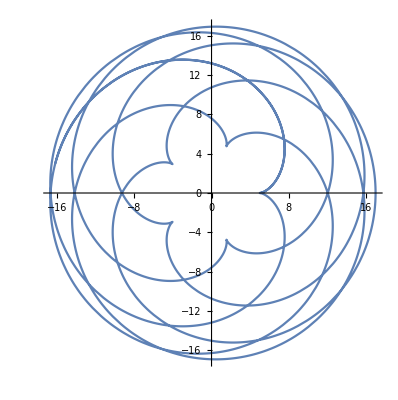

```mathematica
ParametricPlot[{11Cos[t]-6Cos[t*(11/6)],11Sin[t]-6Sin[t*(11/6)]},{t,0,13Pi}]
```

### We’re going to take this pretty, elegant shape, add another coordinate, and then manipulate it in space to add it to throne. We’ll multiply the given equation and add a vector to move it in space. But first, 3D:

```mathematica
ParametricPlot3D[{0, 11Sin[t]-6Sin[t*(11/6)],11Cos[t]-6Cos[t*(11/6)]},{t,0,20Pi},PlotStyle->{Tube[.45]},PlotRange->All,PlotPoints->100]
```

-Graphics3D-

### I wasn’t sure what to do with these piece when I initially saw it, but I knew I wanted it included in the piece somehow. I thought about putting it as the headpiece, until I modified this equation to make an admittedly much more interesting looking piece. But I thought this sort of looked like some family crest or emblem, and thought it was fitting for it to be place into the backing of the throne:

```mathematica
redThroneTest = Show[Graphics3D[
    {RGBColor[.4,0,0],Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Sphere[{ 5.2,1,10},1.5],
    Sphere[{ 5.2,11,10},1.5],
    Sphere[{14.265,1,9.5},1.3],
    Sphere[{14.265,11,9.5},1.3],

   Tube[{{16,-1,24},{16,3,29}},.75],
   Tube[{{16,13,24},{16,9,29}},.75],

  Sphere[{16,-1,23.7},1],
  Sphere[{16,13,23.7},1],
  Sphere[{16,9,29},.8],
  Sphere[{16,3,29},.8],



}}],

ParametricPlot3D[.3{0, 11Sin[t]-6Sin[t*(11/6)],11Cos[t]-6Cos[t*(11/6)]} +{14.75,6,16},{t,0,20Pi},PlotStyle->{Tube[.45]        },PlotRange->All,PlotPoints->100],

Table[Graphics3D[{RGBColor[.7,.7,.7],MeshPrimitives[TransformedRegion[TransformedRegion[RegionResize[discreteCube,1.15],RotationTransform[90Degree,{1,1,0}]],TranslationTransform[{15.4,i,23}]],2]}],{i, -1,13,2}]
]
```

-Graphics3D-

### It looks a bit thicker than when initially spawned because we’ve shrunk it down to .3 of its original size. But this is good; I’m using the method we used for the cubes, “embedding” it into the backing by making it close enough to be considered in the same region. It still needs to pop out and be prominent while still being sturdy, and I couldn’t do that if it was thinner. With that done, let’s move onto the headpiece.

## The Headpiece

### When building this, I knew I mainly wanted a familiar-looking object that also possessed some strange, alien shapes generated with mathematics. When fiddling with the above equation and tweaking values here and there, I came across something that caught my eye and I began toying with. The only modifications made to the emblem above was adding a Cos[t] to the x-coordinate (instead of 0), and changing an 11Cos[t] in the z-coordinate to 11Cos[.5t]. What resulted was this:

```mathematica
ParametricPlot3D[{Cos[t], 11Sin[t]-6Sin[t*(11/6)],11Cos[.5t]-6Cos[t*(11/6)]}, {t,0,20Pi},PlotStyle->{Tube[.7]},PlotRange->All,PlotPoints->100 ]
```

-Graphics3D-

### A pretty strange looking fellow. The head shape and eyes look vaguely like a fly’s. Or maybe if you look at the tendrils around the face it looks like an ode to Cthulhu. Creepy. Anyway, I knew this had to be the headpiece, so I imported it into the throne, again manipulating the size and placement. I wanted it to be a bit oversized to look more imposing and as the dominant feature:

```mathematica
finalThrone = Show[Graphics3D[
    {RGBColor[.4,0,0],Cuboid[{-5,0,-1},{5,12,1}],
    Cuboid[{0,0,1},{5,12,2}],,
    Cuboid[{3,0,2},{6,12,3}],
    
Cuboid[{5,0,-1},{15,2,10}],
    Cuboid[{5,10,-1},{15,12,10}],  
    
Cuboid[{7,2, 8.5},{15,10,9}],
Cuboid[{6,2,3},{7,10,9}],

Tube[{{5,1,10},{14.26,1,9.5}},1.2],
    Tube[{{5,11,10},{14.26,11,9.5}},1.2],
    
Cuboid[{15,0,-1},{17,12,22}],
 Cuboid[{15,-2,22},{17,14,24}],
  {Sphere[{ 5.2,1,10},1.5],
    Sphere[{ 5.2,11,10},1.5],
    Sphere[{14.265,1,9.5},1.3],
    Sphere[{14.265,11,9.5},1.3],

   Tube[{{16,-1,24},{16,3,29}},.75],
   Tube[{{16,13,24},{16,9,29}},.75],

  Sphere[{16,-1,23.7},1],
  Sphere[{16,13,23.7},1],
  Sphere[{16,9,29},.8],
  Sphere[{16,3,29},.8]


}}],

ParametricPlot3D[.3{-.5, 11Sin[t]-6Sin[t*(11/6)],11Cos[t]-6Cos[t*(11/6)]} +{14.75,6,16},{t,0,20Pi},PlotStyle->{Tube[.45],RGBColor[.7,.7,.7]},PlotRange->All,PlotPoints->100],

ParametricPlot3D[.4{Cos[t], 11Sin[t]-6Sin[t*(11/6)],11Cos[.5t]-6Cos[t*(11/6)]} +{15.8,6,31.1},{t,0,20Pi},PlotStyle->{Tube[.7],RGBColor[.7,.7,.7]},PlotRange->All,PlotPoints->100 ],

Table[Graphics3D[{RGBColor[.7,.7,.7],MeshPrimitives[TransformedRegion[TransformedRegion[RegionResize[discreteCube,1.15],RotationTransform[90Degree,{1,1,0}]],TranslationTransform[{15.4,i,23}]],2]}],{i, -1,13,2}]
]
```

-Graphics3D-

### Success! I made the throne itself a deep red and the emblem, headpiece and spikes an off-white to make sure they popped well. Even not colorized, it definitely has better “pop” than my initial prototype. I ended up exporting this as a .stl (which seems to give less issues when uploading) and either a .wrl or .x3d, allowing for printing in color.